# Setup

```mathematica
SetDirectory[NotebookDirectory[]];
Get["C:\\Users\\Miguel\\Github\\Entropy\\Prethermalization\\QMB.wl"];
```

MessageName::messg: TranslationEigenvectorRepresentatives::usage cannot be set to FormatUsage[TranslationEigenvectorRepresentatives[L] returns a list of sublists, each containing:  the decimal representation of a bit-string representative eigenvector,  its pseudomomentum k, and the length of its translation orbit,  for a system of ```L``` qubits.]. It must be set to a string.

MessageName::messg: BlockDiagonalize::usage cannot be set to FormatUsage[BlockDiagonalize[matrix,opts] returns ```matrix``` in block-diagonal form. Only 	option is '''Symmetry'''.]. It must be set to a string.

MessageName::messg: Transform::usage cannot be set to FormatUsage[BlockDiagonalize[matrix,opts] returns ```matrix``` in block-diagonal form. Only 	option is '''Symmetry'''.]. It must be set to a string.

General::stop: Further output of MessageName::messg will be suppressed during this calculation.

SetDelayed::write: Tag Commutator in Commutator[A_,B_] is Protected.

```mathematica
LaunchKernels[14]
```

{Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14)}

```mathematica
Clear[haar];
haar[L_Integer]:=Normalize[Table[RandomVariate[NormalDistribution[0,1]]+I RandomVariate[NormalDistribution[0,1]],{2^L}]];
pageEntropy[La_,Lb_]:=PolyGamma[0,(2^La)(2^Lb)+1]-PolyGamma[0,(2^Lb)+1]-((2^La)-1)/(2*(2^Lb));
```

```mathematica
Clear[sdiag];
sdiag[L_,La_,Lb_,ini_]:=Module[{state=Dyad[ini],dima=2^(La),dimb=2^(Lb),rho},
rho=MatrixPartialTrace[state,2,{dima,dimb}];
Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]]
];
(*haar[L_Integer]:=Normalize[Table[RandomVariate[NormalDistribution[0,1]],{2^L}]];*)
(*Clear[VNentropy];
VNentropy[0|0.]=0;
VNentropy[x_]:=-x*Log[x];*)
Clear[statet];
statet[eigenval_,eigenvec_,transform_,t_,ini_]:=Module[{a,dim=Length[eigenval],inieigen=Conjugate[eigenvec].(Transpose[transform].ini)},
Chop[transform.Total[Exp[-I*eigenval*t]*inieigen*eigenvec]]
];
Clear[evensvn];
evensvn[L_,La_,Lb_,ini_,eigenval_,eigenvec_,transform_,t_]:=Module[{state=statet[eigenval,eigenvec,transform,t,ini],rho,λ,purity,dima=2^(La),dimb=2^(Lb),vn},
rho=MatrixPartialTrace[Dyad[state],2,{dima,dimb}];
Chop[Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]]]
];
Clear[rhoa];
rhoa[ini_,t_,L_,k_,val_,vec_]:=Module[{M,rhoc,rhob,rho,ck=Conjugate[vec] . ini,phases=arrayt[t,val,vec],perm=Delete[Range[L],{k}]},
MatrixPartialTrace[Dyad[N[Total[phases*ck]]],perm,2]];
```

# Test

```mathematica
Get["C:\\Users\\Miguel\\Github\\Entropy\\Prethermalization\\EntanglementWorkflow3.wl"];
```

```mathematica
Names["EntanglementWorkflow3`*"]
```

{buildExpandFullStateFast,buildMaps,compiledEvolverSector,ExpandBlockVector,ExpandFullState,expandFullStateFastTemplate,makeExpansionMatrix,new,ProjectBlockVector,revIndex,VNentropy}

```mathematica
g=1+GoldenRatio^-3;
```

```mathematica
(*2. Parameters*)
L=6;
J=1;
g=1;
hlist=Sort[Append[Table[10^i,{i,-6,0,0.2}],0.0]];
tlist=Developer`ToPackedArray[Table[10^i,{i,-1,8,0.0025}]];
tlist//Length
hlist//Length
```

3601

32

```mathematica
n=Length[hlist]+1;
reds=Table[Blend[{RGBColor[0.1,0.1,1],RGBColor[1,0,0]},t],{t,1/(n-1),1,1/(n-1)}];
cf=Blend[{{0,Blue},{0.5,Purple},{1,Red}},#]&;
```

```mathematica
(*3. Build block maps and compiled fast expander*)
{evenMap,oddMap}=buildMaps[L];
ExpandFullStateFast=buildExpandFullStateFast[evenMap,oddMap,L];
```

```mathematica
(*4. Hamiltonian and evolvers*)
h=hlist[[10]];
Ha=IsingHamiltonian[h,g,J,L,BoundaryConditions->"Open"];
system=BlockDiagonalize[Ha,Symmetry->"Parity"];
{evenEigvals,evenEigvecs}=Transpose[Sort[Transpose[Quiet[Eigensystem[system[[1]]]]]]];
{oddEigvals,oddEigvecs}=Transpose[Sort[Transpose[Quiet[Eigensystem[system[[2]]]]]]];
evenEigvecs=Developer`ToPackedArray[evenEigvecs];
evenEigvals=Developer`ToPackedArray[evenEigvals];
oddEigvecs=Developer`ToPackedArray[oddEigvecs];
oddEigvals=Developer`ToPackedArray[oddEigvals];
evenEvolver=compiledEvolverSector[evenEigvecs,evenEigvals];
oddEvolver=compiledEvolverSector[oddEigvecs,oddEigvals];
(*5. Distribute*)
DistributeDefinitions[evenMap,oddMap,ProjectBlockVector,ExpandFullStateFast,tlist,L,new,evenEvolver,oddEvolver];
```

```mathematica
(*6. Define worker on all kernels*)
ParallelEvaluate[entanglementWorker[state_]:=Module[{psiEven,psiOdd,evenFinal,oddFinal,fullStates},{psiEven,psiOdd}={ProjectBlockVector[state,evenMap,"even",L],ProjectBlockVector[state,oddMap,"odd",L]};
evenFinal=evenEvolver[psiEven,tlist];
oddFinal=oddEvolver[psiOdd,tlist];
fullStates=Table[ExpandFullStateFast[evenFinal[[i]],oddFinal[[i]]],{i,Length[tlist]}];
Map[new[#,L]&,fullStates]];];
```

```mathematica
states=Table[RandomChainProductState[L],{10}];
```

```mathematica
mag=(1/2)IsingHamiltonian[0,1,0,L,BoundaryConditions->"Open"];
```

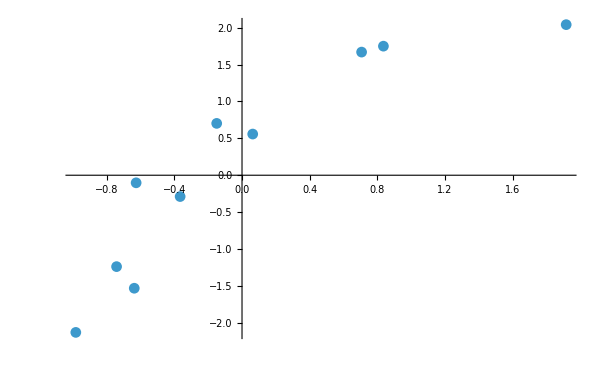

```mathematica
magnetizations=ParallelTable[Chop[Conjugate[i].mag.i],{i,states}];
energies=ParallelTable[Chop[Conjugate[i].Ha.i],{i,states}];
ListPlot[Transpose[{magnetizations,energies}],PlotRange->All,ImageSize->600]
```

```mathematica
(*7. Run computation*)
AbsoluteTiming[data=ParallelTable[entanglementWorker[state],{state,states}];]
```

{0.573732,Null}

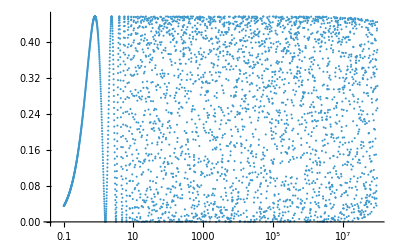

```mathematica
ListLogLinearPlot[Transpose[{tlist,Mean[data]}],PlotRange->All]
```

```mathematica
Clear[haarmagnetized];
haarmagnetized[l_,mz_]:=Module[{nup,dim,sectorIndices,randVec,state},
(*number of spin-up sites*)
nup=Round[mz+l/2];
(*indices of basis states with that magnetization*)
sectorIndices=Select[Range[0,2^l-1],Total[IntegerDigits[#,2,l]]==nup&];
(*dimension of that sector*)
dim=Length[sectorIndices];
(*Haar random complex vector in that sector*)
randVec=RandomVariate[NormalDistribution[],dim]+I RandomVariate[NormalDistribution[],dim];
randVec=Normalize[randVec];
(*full 2^L state with zeros outside the chosen sector*)
state=ConstantArray[0,2^l];
state[[sectorIndices+1]]=randVec;
state];
```

```mathematica
magvalues=Range[-L/2,L/2,1]
```

{-3,-2,-1,0,1,2,3}

```mathematica
Clear[ProjectorsNAList];
(*returns {Π_A(0),Π_A(1),...,Π_A(LA)};each is 2^LA x 2^LA*)
ProjectorsNAList[LA_Integer?NonNegative]:=Module[{d=2^LA,bits,wts},
bits=IntegerDigits[Range[0,2^LA-1],2,LA];(*left-padded LA-bit strings*)
wts=Total/@bits;(*Hamming weights 0..LA*)
Table[With[{idxs=Pick[Range[d],wts,n]},(*indices with weight=n*)SparseArray[Thread[Rule[Transpose[{idxs,idxs}],1]],(*{{i,i}->1,...}*){d,d}]],{n,0,LA}]];
```

```mathematica
La=Lb=L/2;
```

```mathematica
projectors=ProjectorsNAList[La];
```

```mathematica
projectors//Dimensions
```

{4,8,8}

```mathematica
Dimensions/@projectors                   (*all 8x8*)
Tr/@projectors                           (* ->{1,3,3,1}=Binomial[3,n]*)
```

{{8,8},{8,8},{8,8},{8,8}}

{1,3,3,1}

```mathematica
states//Dimensions
```

{10,64}

```mathematica
ini=states[[1]];
```

```mathematica
ini=haar[L];
```

```mathematica
ini=haarmagnetized[L,-1];
```

```mathematica
rho=MatrixPartialTrace[Dyad[ini],2,{2^La,2^Lb}];
```

```mathematica
(*p_{nA}=Tr[Π_nA ρ_A]*)
SectorWeights[rhoA_,projList_List]:=Chop[Tr[#.rhoA]&/@projList,10^(-12)];
(*normalized sector block ρ_A^{(nA)}*)
SectorBlock[rhoA_,proj_]:=Module[{blk=proj.rhoA.proj,p=Chop[Tr[proj.rhoA]]},If[p==0,0,blk/p]];
SectorBlocks[rhoA_,projList_List]:=SectorBlock[rhoA,#]&/@projList;
(*von Neumann entropy of a (sub)density matrix*)
VonNeumannS[m_?MatrixQ]:=Module[{ev=Chop[Eigenvalues[m]]},With[{pos=Select[ev,#>0&]},-Total[pos Log[pos]]]];
(*S=H({p})+Σ p_nA S(ρ_A^{(nA)}) on the block-diagonal (SRE) state*)
SectorEntropySplit[rhoA_,projList_List]:=Module[{ps,blocks,H,Sconf},
ps=SectorWeights[rhoA,projList];
blocks=SectorBlocks[rhoA,projList];
H=With[{p=ps},-Total[Replace[p Log[Replace[p,0->1,{1}]],0.->0.,{1}]]];
Sconf=Total@MapThread[If[#1==0,0,#1*VonNeumannS[#2]]&,{ps,blocks}];
<|"p"->ps,"Snum"->H,"Sconf"->Sconf,"Stotal"->(H+Sconf)|>];
```

```mathematica
entropies=Chop[SectorEntropySplit[rho,projectors]]
```

<|p→{0.209124,0.686054,0.104822,0},Snum→0.822172,Sconf→0.50826,Stotal→1.33043|>

```mathematica
(*for your evolved ρ_A at some time t*)
res=SectorEntropySplit[rho,projectors];
res["p"]; (*{p_0,p_1,...,p_La}*)
res["Stotal"]; (* =Snum+Sconf*)
```

```mathematica
rhoADeph=Total[(#.rho.#)&/@projectors];
SectorEntropySplit[rhoADeph,projectors]
```

<|p→{0.209124,0.686054,0.104822,0},Snum→0.822172,Sconf→0.50826,Stotal→1.33043|>

```mathematica
(*assuming:projList is your {Π_0,Π_1,...,Π_LA} and rho is ρ_A*)
blockInfo=Table[Module[{P=projectors[[n+1]],r,p},
p=Tr[P.rho];
r=If[p==0,0,P.rho.P/p];
{n,p,If[r===0,0,MatrixRank[r]],If[r===0,0,VonNeumannS[r]]}],{n,0,La}];
```

```mathematica
Grid[Prepend[Chop[blockInfo],{"nA","p_nA","rank(ρ_nA)","S(ρ_nA)"}],Frame->All]
```

nA | p_nA | rank(ρ_nA) | S(ρ_nA)
0 | 0.209124 | 1 | 0
1 | 0.686054 | 3 | 0.740845
2 | 0.104822 | 1 | 0
3 | 0 | 0 | 0

```mathematica
magA=(1/2)IsingHamiltonian[0,1,0,L/2,BoundaryConditions->"Open"];
```

```mathematica
(*Q_A=(1/2) Sum σ^z_i on A:build once,then*)
CommutatorNorm=Norm[rho.magA-magA.rho,"Frobenius"]
```

0.

```mathematica
SectorSpectra[rho_,projList_List]:=Table[Module[{P=projList[[n+1]],p},
p=Tr[P.rho];
If[p==0,{n,{}},{n,ReverseSort[Chop[Eigenvalues[(P.rho.P)/p]]]}]],{n,0,La}];
```

```mathematica
rhoDeph=Total[(#.rho.#)&/@projectors];
{Stotal,StotalDeph,coherenceGap}=Chop[{VonNeumannS[rho],VonNeumannS[rhoDeph],VonNeumannS[rhoDeph]-VonNeumannS[rho]}]
```

{1.33043,1.33043,0}

```mathematica
(*assumes:La,projectors={Π0,Π1,...,Π_La},rho,VonNeumannS*)
blockInfo=Table[Module[{P=projectors[[n+1]],p,r,rank,Sblk,numC,confC},p=Tr[P.rho];
r=If[p==0,0,P.rho.P/p];
rank=If[r===0,0,MatrixRank[r]];
Sblk=If[r===0,0,VonNeumannS[r]];
numC=If[p==0,0,-p Log[p]];(*per-sector number contribution*)confC=p*Sblk;(*per-sector configurational contribution*){n,p,rank,Sblk,numC,confC}],{n,0,La}];
```

```mathematica
(*column sums (for a quick check:Sum[numC]=Snum,Sum[confC]=Sconf)*)
sumNumC=Total[blockInfo[[All,5]]];
sumConfC=Total[blockInfo[[All,6]]];
sumBoth=sumNumC+sumConfC;
Grid[Join[{{"nA","p_nA","rank(ρ_nA)","S(ρ_nA)","S classic","S configuration"}},Chop[blockInfo]],Frame->All]
```

nA | p_nA | rank(ρ_nA) | S(ρ_nA) | S classic | S configuration
0 | 0.157567 | 1 | 0 | 0.291169 | 0
1 | 0.377707 | 3 | 0.89436 | 0.367749 | 0.337806
2 | 0.36693 | 3 | 0.986731 | 0.367878 | 0.362061
3 | 0.0977963 | 1 | 0 | 0.227364 | 0

```mathematica
(*column sums (for a quick check:Sum[numC]=Snum,Sum[confC]=Sconf)*)
sumNumC=Total[blockInfo[[All,5]]];
sumConfC=Total[blockInfo[[All,6]]];
sumBoth=sumNumC+sumConfC;
Grid[Join[{{"nA","p_nA","rank(ρ_nA)","S(ρ_nA)","S classic","S configuration"}},Chop[blockInfo]],Frame->All]
```

nA | p_nA | rank(ρ_nA) | S(ρ_nA) | S classic | S configuration
0 | 0.197418 | 1 | 0 | 0.320298 | 0
1 | 0.461534 | 1 | 0 | 0.356858 | 0
2 | 0.290957 | 1 | 0 | 0.35921 | 0
3 | 0.0500912 | 1 | 0 | 0.149969 | 0

```mathematica
(*column sums (for a quick check:Sum[numC]=Snum,Sum[confC]=Sconf)*)
sumNumC=Total[blockInfo[[All,5]]];
sumConfC=Total[blockInfo[[All,6]]];
sumBoth=sumNumC+sumConfC;
Grid[Join[{{"nA","p_nA","rank(ρ_nA)","S(ρ_nA)","S classic","S configuration"}},Chop[blockInfo]],Frame->All]
```

nA | p_nA | rank(ρ_nA) | S(ρ_nA) | S classic | S configuration
0 | 1. | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
2 | 0 | 0 | 0 | 0 | 0
3 | 0 | 0 | 0 | 0 | 0

```mathematica
(*column sums (for a quick check:Sum[numC]=Snum,Sum[confC]=Sconf)*)
sumNumC=Total[blockInfo[[All,5]]];
sumConfC=Total[blockInfo[[All,6]]];
sumBoth=sumNumC+sumConfC;
Grid[Join[{{"nA","p_nA","rank(ρ_nA)","S(ρ_nA)","S classic","S configuration"}},Chop[blockInfo]],Frame->All]
```

nA | p_nA | rank(ρ_nA) | S(ρ_nA) | S classic | S configuration
0 | 0.72564 | 1 | 0 | 0.232714 | 0
1 | 0.27436 | 1 | 0 | 0.354834 | 0
2 | 0 | 0 | 0 | 0 | 0
3 | 0 | 0 | 0 | 0 | 0

```mathematica
(*Q_A=(1/2) Sum σ^z_i on A:build once,then*)
CommutatorNorm=Norm[rho.magA-magA.rho,"Frobenius"]
```

0.

```mathematica
(*column sums (for a quick check:Sum[numC]=Snum,Sum[confC]=Sconf)*)
sumNumC=Total[blockInfo[[All,5]]];
sumConfC=Total[blockInfo[[All,6]]];
sumBoth=sumNumC+sumConfC;
Grid[Join[{{"nA","p_nA","rank(ρ_nA)","S(ρ_nA)","S classic","S configuration"}},Chop[blockInfo]],Frame->All]
```

nA | p_nA | rank(ρ_nA) | S(ρ_nA) | S classic | S configuration
0 | 0.209124 | 1 | 0 | 0.327243 | 0
1 | 0.686054 | 3 | 0.740845 | 0.258504 | 0.50826
2 | 0.104822 | 1 | 0 | 0.236425 | 0
3 | 0 | 0 | 0 | 0 | 0